```mathematica
Clear["Global`*"];
cl=4250; ct=0.47 cl; cf=1500; d=0.0005; r0m=0.12;
ctl=ct/cl;cfl=cf/cl;cft=cf/ct;
F1[ξ_,Ω_]:=((2-ξ^2)^2-4 √(1-ξ^2)√(1-ctl^2 ξ^2))Sin[Ω/2/ξ √(ξ^2/cft^2-1)]-r0m ξ^4 √(1-ctl^2 ξ^2)/√(ξ^2/cft^2-1)Cos[Ω/2/ξ √(ξ^2/cft^2-1)];
F2[ξ_,Ω_]:=((2-ξ^2)^2-4 √(1-ξ^2)√(1-ctl^2 ξ^2))Sin[Ω/2/ξ √(ξ^2/cft^2-1)]+r0m ξ^4 √(1-ctl^2 ξ^2)/√(ξ^2/cft^2-1)Cos[Ω/2/ξ √(ξ^2/cft^2-1)];
```

```mathematica
FindRoot[F2[xx,4.5]==0,{xx,1-2.5I}]
```

{xx→0.319967-2.31068 ⅈ}

```mathematica
ans={};
(*x0=0.843734+0.32779I;*)
Do[
x0=(x/.FindRoot[F2[x,Ω]==0,{x,x1-I x2}]);
If[Re[x0]>0&&Im[x0]<-10^-5,
ans=Join[ans,{{Ω(1+I),x0}}]]
,{Ω,0.01,6.01,0.01},{x1,0.1,0.9,0.1},{x2,0.1,0.9,0.1}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

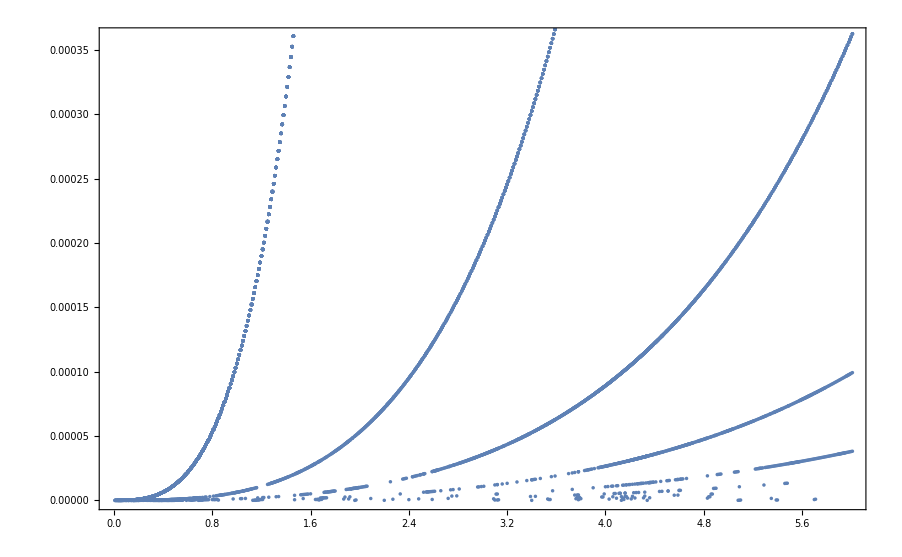

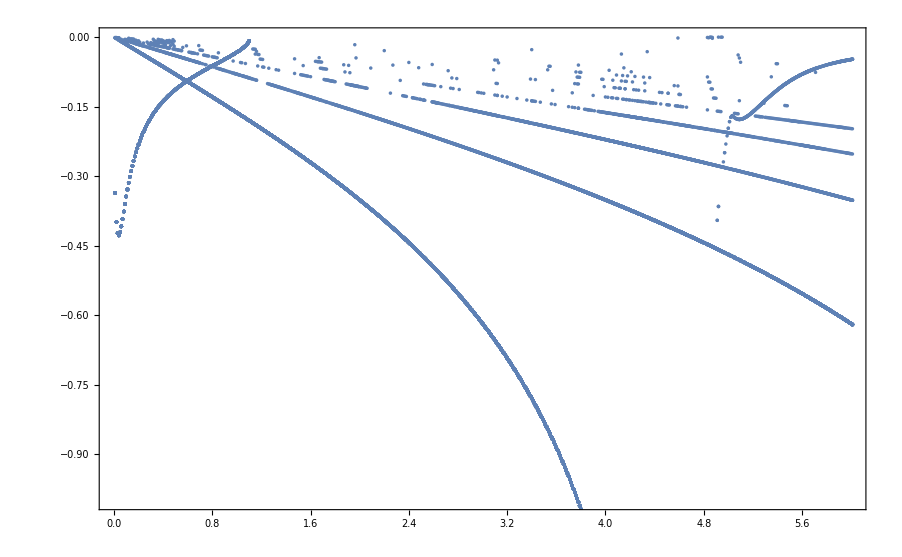

```mathematica
ListPlot[Re[ans],Joined->False,PlotRange->{{0,6},{0,0.00036}},Frame->True]
ListPlot[Im[ans],Joined->False,PlotRange->{{0,6},{-1,0}},Frame->True]
```

```mathematica
1:{0.005990914683052318-0.6184699988591529 ⅈ,3}
2:{0.0029969653761461657-0.6185755109028361 ⅈ,6}
3:{0.000360307908528874-0.35144413233821226 ⅈ,6}
```

```mathematica
findLine[ΩΩ_,ξξ_]:=Module[{Ω0=ΩΩ,ξ0=ξξ},
left={};

stepΩ=-0.01;
o=Ω0;x=ξ0;slp=0;
While[o>Abs[stepΩ]&&Re[x]>0&&Im[x]<0,
xnew=ξ/.FindRoot[F2[ξ,o+stepΩ]==0,{ξ,x+slp stepΩ}];
slp=(xnew-x)/stepΩ;
o=o+stepΩ;
left=Join[{{o,Re[xnew],Im[xnew]}},left];
x=xnew;
];

right={};
stepΩ=0.01;
o=Ω0;x=ξ0;slp=0;
While[o<7&&Re[x]>0&&Im[x]<0,
xnew=ξ/.FindRoot[F2[ξ,o+stepΩ]==0,{ξ,x+slp stepΩ}];
slp=(xnew-x)/stepΩ;
o=o+stepΩ;
right=Join[right,{{o,Re[xnew],Im[xnew]}}];
x=xnew;
];

Join[left,{{ΩΩ,Re[ξξ],Im[ξξ]}},right]]
```

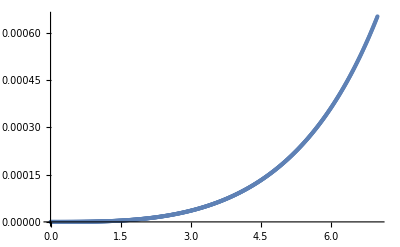

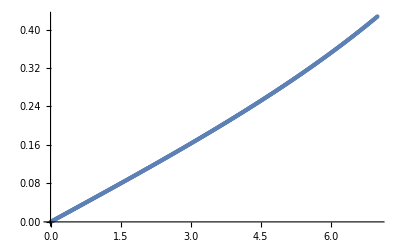

```mathematica
t=findLine[6,0.000360307908528874-0.35144413233821226 ⅈ];
t1=Table[{x[[1]],x[[2]]},{x,t}];t2=Table[{x[[1]],-x[[3]]},{x,t}];
ListPlot[t1,PlotRange->All]
ListPlot[t2,PlotRange->All]
```

```mathematica
Export["C:\\Users\\Andri_000\\Documents\\t.csv",Abs[t],"CSV"]
```

C:\Users\Andri_000\Documents\t.csv